```mathematica
Map[h,{x1,x2,x3,α}]
```

{h[x1],h[x2],h[x3],h[α]}

```mathematica
h/@ k[x1,x2,x3]
```

k[h[x1],h[x2],h[x3]]

```mathematica
Head/@{1,1/2,True,"number",a+b,a-b,a*b,a/b,(f+g)[x1,x2,x3]}
```

{Integer,Rational,Symbol,String,Plus,Plus,Times,Times,f+g}

```mathematica
Head[ex]
```

Symbol

```mathematica
myAtomQ=Function[ex,MemberQ[{Symbol,Integer,Rational,Reals,Complex,String,Image},Head[ex]]]
```

Function[ex,MemberQ[{Symbol,Integer,Rational,ℝ,Complex,String,Image},Head[ex]]]

```mathematica
ex=f[x1,x2,x3]
```

f[x1,x2,x3]

```mathematica
List@@ex
```

{x1,x2,x3}

```mathematica
Apply[g,ex]
```

g[x1,x2,x3]

```mathematica
List[1,2,3]
```

{1,2,3}

```mathematica
ex=h[1,2,3]
seq=Sequence@@ex
lst=List@@ex
```

h[1,2,3]

Sequence[1,2,3]

{1,2,3}

```mathematica
f[seq]
f[lst]
f@@lst
f[seq,lst,4,5,6]
```

f[1,2,3]

f[{1,2,3}]

f[1,2,3]

f[1,2,3,{1,2,3},4,5,6]

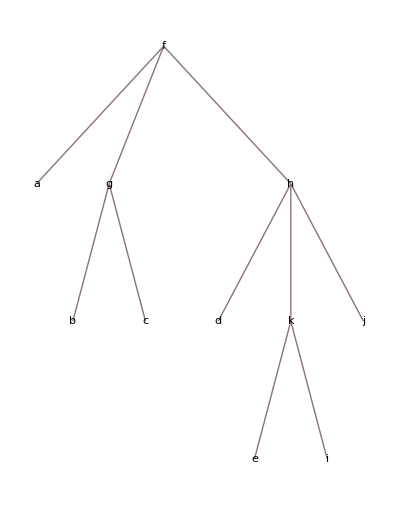

```mathematica
TreeForm[ex=f[a,g[b,c],h[d,k[e,i],j]]]
```

```mathematica
ex[[3]]
```

h[d,k[e,i],j]

```mathematica
ex[[3]][[2]][[2]]
```

i

```mathematica
ex[[-1,-2,-1]]
```

i

```mathematica
ex[[{2,3}]]
```

f[g[b,c],h[d,k[e,i],j]]

```mathematica
ex[[2;;3]]
```

f[g[b,c],h[d,k[e,i],j]]

```mathematica
ex[[1;;3;;2]]
```

f[a,h[d,k[e,i],j]]

```mathematica
%
```

f[a,h[d,k[e,i],j]]

```mathematica
%30
```

i

```mathematica
Range[1,10]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
%[[1;;-3;;4]]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
Take[%41,{2,4}]
```

{2,3,4}

```mathematica
Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
Range[2,10]
```

{2,3,4,5,6,7,8,9,10}

```mathematica
Range[3,10,3]
```

{3,6,9}

```mathematica
Table[i^2+i+1,{i,10}]
```

{3,7,13,21,31,43,57,73,91,111}

```mathematica
Table[KroneckerDelta[i,j-1]+t KroneckerDelta[i,j+4],{i,5},{j,5}]
```

{{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1},{t,0,0,0,0}}

```mathematica
Array[#^2+#+1&,10]
#^2+#+1&/@Range[10]
```

{3,7,13,21,31,43,57,73,91,111}

{3,7,13,21,31,43,57,73,91,111}

```mathematica
Array[f,5,2]
```

{f[2],f[3],f[4],f[5],f[6]}

```mathematica
Array[g,%]
```

Array::ilsmn: 在 Array[g,{f[2],f[3],f[4],f[5],f[6]}] 的位置 2 处应该是单个机器精度非负整数或者由机器精度非负整数组成的列表.

Array[g,{f[2],f[3],f[4],f[5],f[6]}]

```mathematica
h@@%55
```

h[f[2],f[3],f[4],f[5],f[6]]

```mathematica
Tuples[Range[3],3]
Outer[f,Range[3],Range[4]]//MatrixForm
```

{{1,1,1},{1,1,2},{1,1,3},{1,2,1},{1,2,2},{1,2,3},{1,3,1},{1,3,2},{1,3,3},{2,1,1},{2,1,2},{2,1,3},{2,2,1},{2,2,2},{2,2,3},{2,3,1},{2,3,2},{2,3,3},{3,1,1},{3,1,2},{3,1,3},{3,2,1},{3,2,2},{3,2,3},{3,3,1},{3,3,2},{3,3,3}}

(f[1,1] | f[1,2] | f[1,3] | f[1,4]
f[2,1] | f[2,2] | f[2,3] | f[2,4]
f[3,1] | f[3,2] | f[3,3] | f[3,4])

```mathematica
FreeQ[{{1,1,3,0},{2,1,2,2}},0]
FreeQ[{{1,1,3,0},{2,1,2,2}},0,2]
```

False

False

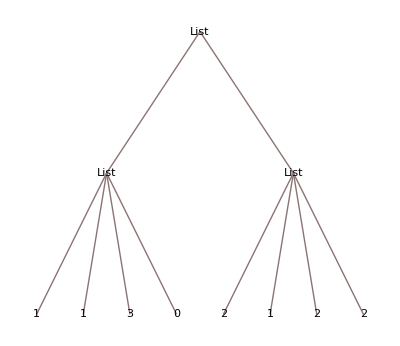

```mathematica
TreeForm[{{1,1,3,0},{2,1,2,2}}]
```

```mathematica
euler = (a+b^n)/n==x
{Count[euler,n],Count[euler,n,4]}
```

(a+b^n)/n==x

{0,2}

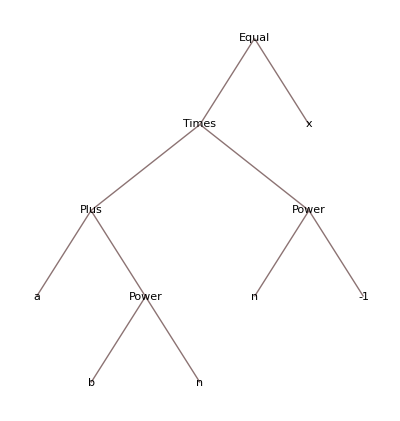

```mathematica
TreeForm[euler]
```

```mathematica
Position[euler,n]
```

{{1,1,2,2},{1,2,1}}

```mathematica
Select[Prime/@Range[10],OddQ]
Select[Prime/@Range[10],Mod[#,4]==1&]
```

{3,5,7,11,13,17,19,23,29}

{5,13,17,29}

```mathematica
list=Array[RandomInteger[10]&,{20,2}]
```

{{5,3},{7,6},{6,10},{6,1},{6,5},{9,4},{4,1},{6,7},{2,9},{8,4},{8,2},{8,5},{2,5},{10,9},{10,0},{3,1},{4,10},{5,4},{2,2},{5,5}}

```mathematica
g[#,#^2]&/@{x,y,z}
```

{g[x,x^2],g[y,y^2],g[z,z^2]}

```mathematica
Tan'
```

Sec[#1]^2&

```mathematica
Function[u,u+3][x]
```

3+x

```mathematica
Function[3+#][x]
```

3+x

```mathematica
(#1^2+#2^4)&[x,y]
```

x^2+y^4

```mathematica
3+#&[x]
```

3+x

```mathematica
f=(3+#)&
```

3+#1&

```mathematica
{f[a],f[b]}
```

{3+a,3+b}

```mathematica
Select[{1,-1,2,-2,3},#>0&]
```

{1,2,3}

```mathematica
FullForm[#>0&]
```

Function[Greater[Slot[1],0]]

```mathematica
Slot[1]
```

#1

```mathematica
Array[1+#^2&,10]
```

{2,5,10,17,26,37,50,65,82,101}

```mathematica
Sort[{{a,2},{c,1},{d,3}},#1[[2]]<#2[[2]]&]
```

{{c,1},{a,2},{d,3}}

```mathematica
Nearest[{1,2,4,5,8,16},1.5,DistanceFunction->((#1-#2)^2&)]
```

{1,2}

```mathematica
FullForm[DistanceFunction->((#1-#2)^2&)]
```

Rule[DistanceFunction,Function[Power[Plus[Slot[1],Times[-1,Slot[2]]],2]]]

```mathematica
Function[x,x^2]'
```

Function[x,2 x]

```mathematica
FullForm[(x^2)']
```

Derivative[1][Power[x,2]]

```mathematica
Derivative[1][Power[x,2]]
```

(x^2)'

```mathematica
f=D[(#^2),#]&
```

∂_#1 #1^2&

```mathematica
D[x^2,x]
```

2 x

```mathematica
f[x]
```

2 x

```mathematica
Limit[(1+I*Pi/n)^n,{n->Infinity}]
```

-1

```mathematica
For[i=0,i<4,i++,Print[i]]
```

```mathematica
Integrate[Log[x^3+1]/(x^2+1),{x,0,Infinity}]
```

1/12 (-4 Catalan+π (Log[8]+8 Log[2+√3]))

```mathematica
N[1/12 (-4 Catalan+π (Log[8]+8 Log[2+√3]))]
```

2.9973

```mathematica
NumberForm[2.9973048272275395,16]
```

2.99730482722754

```mathematica
Catalan
```

Catalan

```mathematica
N[Catalan,10]
```

0.9159655942

```mathematica
f[n_]:=Integrate[(x^n+y^n)^(-1+1/n),{x,1,Infinity},{y,1,Infinity}]
```

```mathematica
f[3]
```

Integrate::idiv: (-3 (-(1+x)/(«1»))^(1/3) (1+(«1»)^(«1») x) ((«1»)/(«1»))^(2/3) Hypergeometric2F1[1/3,2/3,4/3,((1-ⅈ Power[«2»]) (1+Power[«2»] x))/(2 (1+x))]+«1»)/x 的积分在 {1,∞} 上不收敛.

∫_1^∞ 1/x(-3 (-(1+x)/(-1+(-1)^(2/3)))^(1/3) (1+(-1)^(2/3) x) (((-1)^(2/3)+x)/((1+(-1)^(1/3)) (1+x^3)))^(2/3) Hypergeometric2F1[1/3,2/3,4/3,((1-ⅈ √3) (1+(-1)^(2/3) x))/(2 (1+x))]+378 (-2)^(2/3) (1+ⅈ √3)^(1/3) Hypergeometric2F1[1/3,2/3,4/3,1/2 (1-ⅈ √3)] Root7.84 × 10^-4-2.15 × 10^-3 ⅈRoot[1+144027072 #1^3+6914599156297728 #1^6&,3]0.0007835929437196398)ⅆx

```mathematica
N[Sin[1],10]
```

0.8414709848

```mathematica
Integrate[Cos[x]/(Exp[1/x]+1),{x,-1,1}]
```

Sin[1]

```mathematica
WolframAlpha["int -(t-Tanh[t])Sech[t]^2Tanh[t] over t",IncludePods->"IndefiniteIntegral",AppearanceElements->{"Pods"},PodStates->{"IndefiniteIntegral__Step-by-step solution"}]
```

WolframAlphaQueryResults

```mathematica
Integrate[Log[x]/(1+x^2),{x,0,1}]
```

-Catalan

```mathematica
Integrate[1/(x^2+x+1),x]
```

(2 ArcTan[(1+2 x)/(√3)])/(√3)

```mathematica
Integrate[Sin[x]/x,{x,0,Infinity}]
```

π/2

```mathematica
WolframAlpha["int Sin[x]/x over x from 0 to Pi",IncludePods->"IndefiniteIntegral",AppearanceElements->{"Pods"},PodStates->{"IndefiniteIntegral__Step-by-step solution"}]
```

WolframAlphaQueryResults

```mathematica
Integrate[Log[x]/(b^2+x^2)-Log[x]/(b^2 x^2 + 1),{x,0,1}]
```

ConditionalExpression[1/(2 √(-b^2))(-PolyLog[2,-1/(√(-b^2))]+PolyLog[2,1/(√(-b^2))]-PolyLog[2,-√(-b^2)]+PolyLog[2,√(-b^2)]), Im[√(-b^2)]≠0&&Re[b]≠0]

```mathematica
Integrate[Sqrt[x]/(x^2+a^2),{x,0,Infinity}]
```

ConditionalExpression[((1/a^2)^(1/4) π)/(√2), Re[a^2]≥0||a^2∉ℝ]

```mathematica
1/(x^3-1)//Apart
```

1/(3 (-1+x))+(-2-x)/(3 (1+x+x^2))

```mathematica
Solve[{a+b==0,a-b+c==0,a-c==1},{a,b,c}]
```

{{a→1/3,b→-1/3,c→-2/3}}

```mathematica
x^4(1-x)^4/(1+x^2)//Apart
```

4-4 x^2+5 x^4-4 x^5+x^6-4/(1+x^2)

有理函数
Wolfram 语言可以有效地处理单变量和多变量的有理函数，通过内置函数直接执行标准的代数变换.

Apart — 分解成为最小分母的部分分式
Together — 通分求和
Cancel — 约去分子、分母的公因式
Numerator, Denominator — 选取分子，分母
NumeratorDenominator ▪  PolynomialRemainder ▪  PolynomialQuotient

Factor — 因式分解
Expand — 除分母外的因式展开
ExpandAll — 全部因式展开，包括分母
ExpandNumerator, ExpandDenominator — 只展开分子和分母
PadeApproximant — 求出函数的一个有理近似值
有理函数的运算
Residue ▪  Integrate ▪  Sum

```mathematica
Integrate[(x(1-x))^16/(1+x^2),{x,0,1}]
```

-5930158704872/29494189725+64 π

```mathematica
N[5930158704872/(29494189725 64),24]
 N[Pi,24]
```

3.14159265358916382301125

3.14159265358979323846264

```mathematica
N[355/113,24]
 N[Pi,24]
```

3.14159292035398230088496

3.14159265358979323846264

```mathematica
Integrate[1/(x-2),{x,4,8}]
```

Log[3]

```mathematica
Integrate[1/(x-1)^(2/3),{x,0,3}]
```

-3 (-1)^(1/3)+3 2^(1/3)

```mathematica
Integrate[1/Sqrt[x^3-1],{x,1,Infinity}]
```

(2 √π Gamma[7/6])/Gamma[2/3]

```mathematica
N[(2 √π Gamma[7/6])/Gamma[2/3]]
```

2.42865

```mathematica
Integrate[Sin[x]^2/(Sin[x] + Cos[x]),{x,0,Pi/2}]
```

ArcTanh[1/(√2)]/(√2)

```mathematica
N[ArcTanh[1/(√2)]/(√2)]
```

0.623225

```mathematica
1/2/Sqrt[2] *Log[3+2Sqrt[2]]//N
```

0.623225

```mathematica
ArcTanh[x]
```

ArcTanh[x]

```mathematica
Simplify[TrigToExp[ArcTanh[x]]]
```

1/2 (-Log[1-x]+Log[1+x])

2023.5.6

```mathematica
Integrate[Exp[-t x]*Sin[s x],x]
```

-(ⅇ^(-t x) (s Cos[s x]+t Sin[s x]))/(s^2+t^2)

```mathematica
Integrate[Log[x]^2,{x,0,1}]
```

2

```mathematica
Integrate[Sqrt[x]*Log[x]^2,{x,0,1}]
```

16/27

```mathematica
D[ArcSin[b],b]
```

1/(√(1-b^2))

```mathematica
D[Log[1+Sqrt[1-b^2]],b]
```

-b/(√(1-b^2) (1+√(1-b^2)))

23.5.7

```mathematica
Integrate[1/(1+x^2)^2,{x,0,Infinity}]
```

π/4

```mathematica
Integrate[(a^2-x^2)x Integrate[E^(-c y),{y,a-x,a+x}],{x,0,a}]
```

(4 ⅇ^(-a c) (-3 a c Cosh[a c]+(3+a^2 c^2) Sinh[a c]))/c^5

```mathematica
Simplify[TrigToExp[(4 ⅇ^(-a c) (-3 a c Cosh[a c]+(3+a^2 c^2) Sinh[a c]))/c^5]]
```

(ⅇ^(-2 a c) (6 (-1+ⅇ^(2 a c))+2 a^2 c^2 (-1+ⅇ^(2 a c))-6 a c (1+ⅇ^(2 a c))))/c^5

```mathematica
ⅇ^(-2 a c) (6 (-1+ⅇ^(2 a c))+2 a^2 c^2 (-1+ⅇ^(2 a c))-6 a c (1+ⅇ^(2 a c)))//Expand
```

6-6 a c+2 a^2 c^2-6 ⅇ^(-2 a c)-6 a c ⅇ^(-2 a c)-2 a^2 c^2 ⅇ^(-2 a c)

```mathematica
Integrate[Integrate[(a^2-x^2)x Integrate[E^(-c y),{y,a-x,a+x}],{x,0,a}],c]
```

-(3+2 a^2 c^2-3 ⅇ^(-2 a c)+a c (-4-2 ⅇ^(-2 a c)))/(2 c^4)

```mathematica
1/c^2*(a^2-3 a/c + 1/c*(a+3/2/c)(1-E^(-2a c)))
```

(a^2-(3 a)/c+((a+3/(2 c)) (1-ⅇ^(-2 a c)))/c)/c^2

```mathematica
FullSimplify[(a^2-(3 a)/c+((a+3/(2 c)) (1-ⅇ^(-2 a c)))/c)/c^2]
```

(ⅇ^(-2 a c) (-3-2 a c+(3+2 a c (-2+a c)) ⅇ^(2 a c)))/(2 c^4)

```mathematica
FullSimplify[ⅇ^(-2 a c) (-3-2 a c+(3+2 a c (-2+a c)) ⅇ^(2 a c))]
```

3-4 a c+2 a^2 c^2-(3+2 a c) ⅇ^(-2 a c)

```mathematica
3+2 a^2 c^2-3 ⅇ^(-2 a c)+a c (-4-2 ⅇ^(-2 a c))//FullSimplify
```

3-4 a c+2 a^2 c^2-(3+2 a c) ⅇ^(-2 a c)

```mathematica
Integrate[1/Sqrt[x^3-1],x]
```

(x √(1-x^3) Hypergeometric2F1[1/3,1/2,4/3,x^3])/(√(-1+x^3))

```mathematica
Integrate[1/Sqrt[x^3-1],{x,1,Infinity}]
```

(2 √π Gamma[7/6])/Gamma[2/3]

```mathematica
N[(2 √π Gamma[7/6])/Gamma[2/3]]
```

2.42865